```mathematica
Length[Subsets[Range[5]]]
```

32

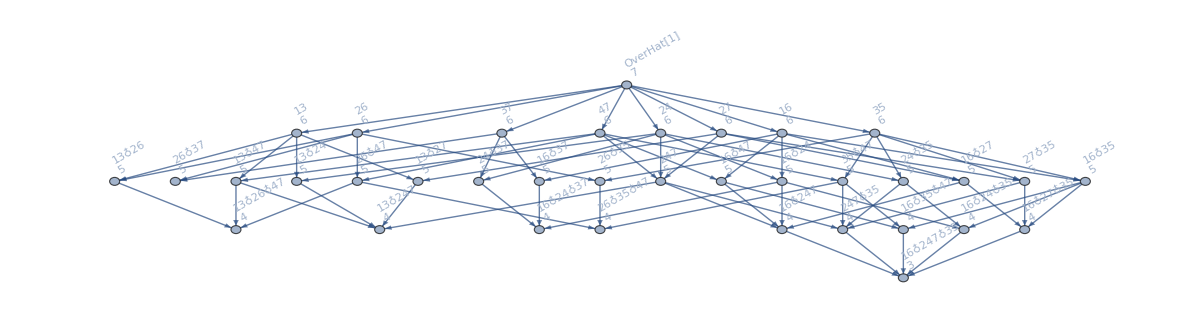
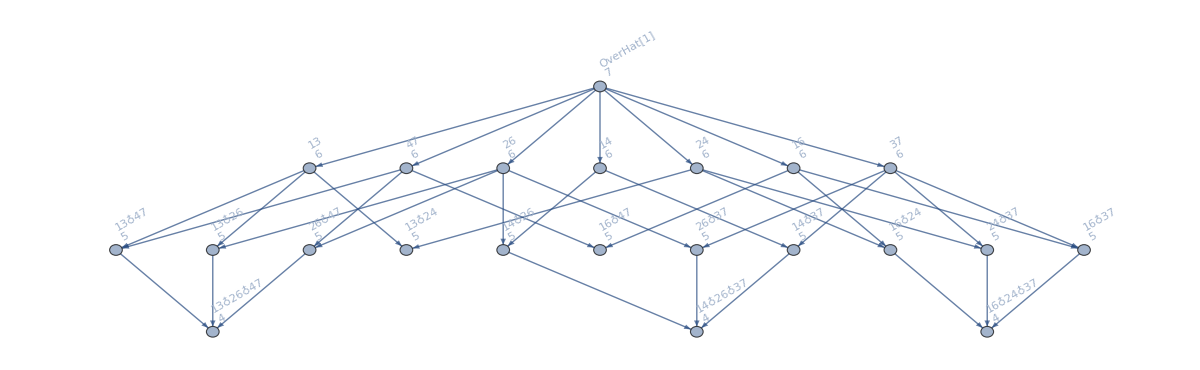
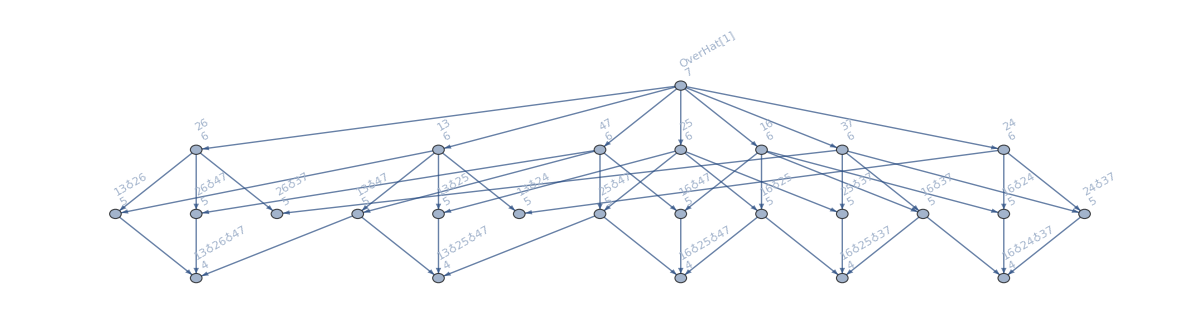
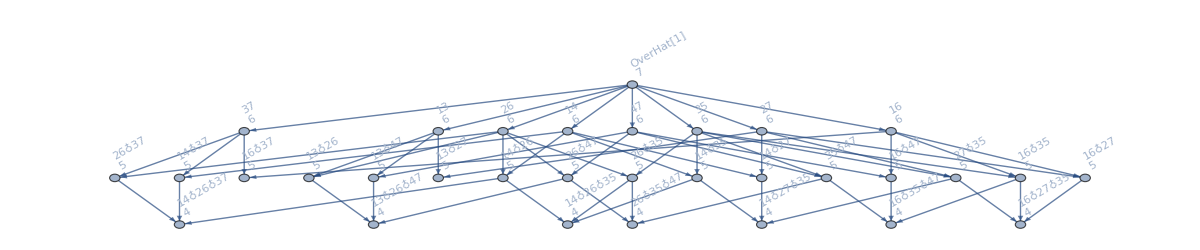
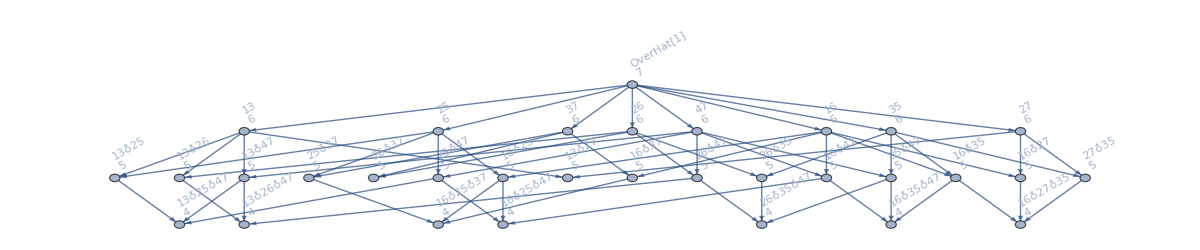
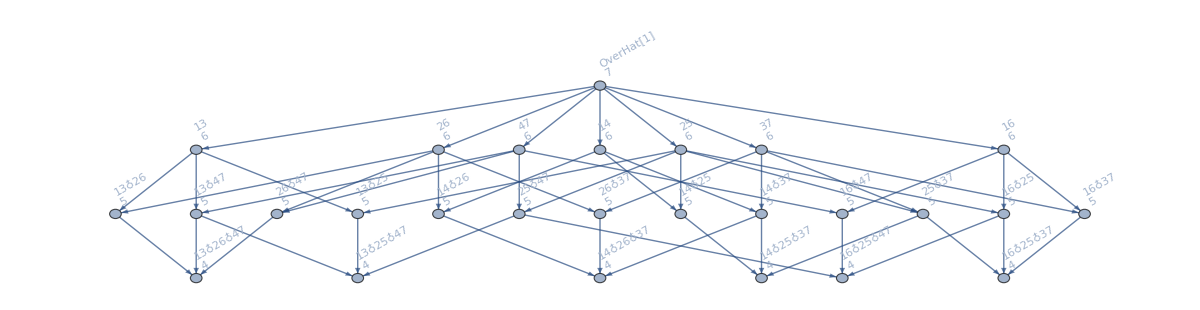
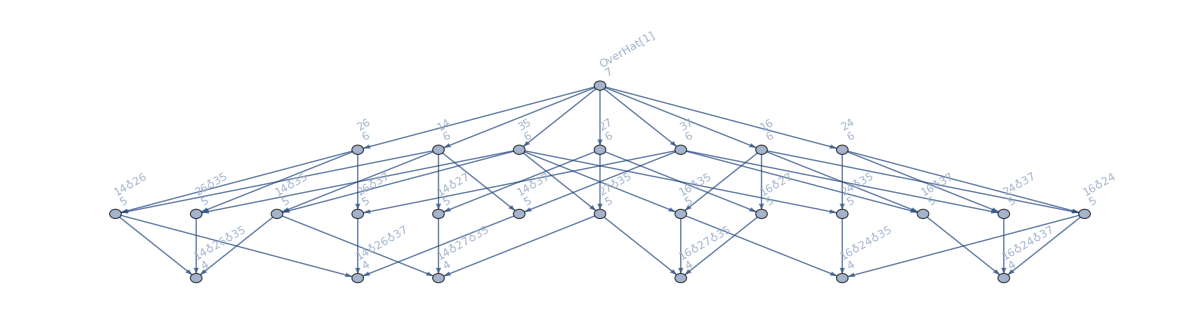
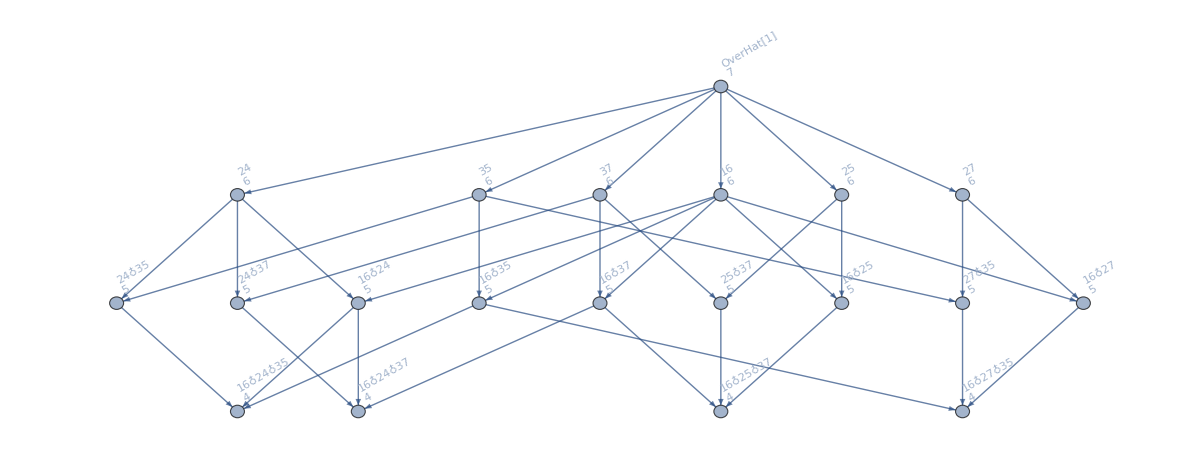
{-Graphics-{1,2,3},-Graphics-{1,2,4},-Graphics-{1,2,5},-Graphics-{1,3,4},-Graphics-{1,3,5},-Graphics-{1,4,5},-Graphics-{2,3,4},-Graphics-{2,3,5},-Graphics-{2,4,5},-Graphics-{3,4,5},-Graphics-{1,2,3,4},-Graphics-{1,2,3,5},-Graphics-{1,2,4,5},-Graphics-{1,3,4,5},-Graphics-{2,3,4,5},-Graphics-{1,2,3,4,5}}

```mathematica
Table[
With[{formula=GAll[sample]},
Labeled[
Graph[FormulaGraphReverse2[formula],VertexStyle->Join[
Map[#->Yellow&,Select[formula,With[{sets=SymbolToSets[#]},
Length[sets]≥3&&HasTrianglePattern[sets]]&]],
Map[#->Brown&,Select[formula,With[{sets=SymbolToSets[#]},
Length[sets]≥4&&HasQuadrilateralPattern[sets]]&]]
],ImageSize->1200],
sample
]
]
,{sample,Subsets[Range[5],{3,5}]}]
```